# DAQ Simulation

## ADC

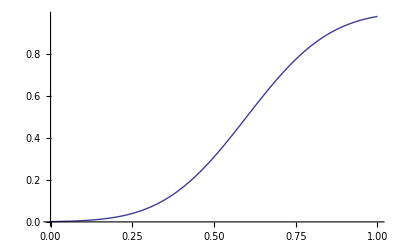

```mathematica
Spec[x_]:=CDF[NormalDistribution[0.6,0.2],x]
Plot[Spec[x],{x,0,1}]
```

```mathematica
RawSignal[chance_,thershold_,num_]:=Table[If[Random[Real,{0,1}]>(1-chance),Spec[Random[Real,{thershold,1}]],0],{i,1,num}]
```

36

0.52063

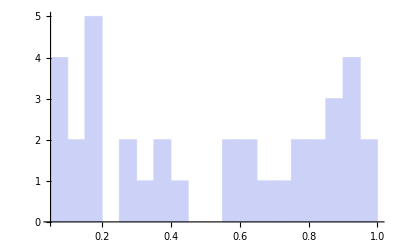

```mathematica
A=RawSignal[0.04,0.3,1000];
Length[A]-Count[A,0]
CutA=DeleteCases[A,0];
Mean[CutA]
Histogram[CutA,20]
```

## TDC

```mathematica
TrueEvent[chance_,num_,div_]:=Table[Table[If[i==1,If[Random[Real,{0,1}]≥ (1-chance),1,0],0],{i,1,div}],{i, 1, num}]
AcciEvent[chance_,num_, div_]:=Table[
If[Random[Real,{0,1}]≥ (1-chance),1,0](a=Table[0,{i,1,div}];a[[Random[Integer,{1,div}]]]=1;Table[a[[i]],{i,1,div}]),{i,1, num}]
```

```mathematica
Clear[TrueEvent, AcciEvent,a]
```

```mathematica
DisplayArray[A_,B_,T_]:=ArrayPlot[Transpose[(T+(A/4)+(B/2))],ImageSize->3 Length[T],ColorRules->{1->Blue,1/4->Green,1/2->Cyan,5/4->Orange,3/2->Purple,3/4->Red}]
DisplayList[A_,B_,T_]:=Show[
ListPlot[Flatten[T],Filling->Axis,FillingStyle->Blue,PlotRange->{0,1},ImageSize->3Length[T],AspectRatio->100/(3Length[T])],
ListPlot[Flatten[A],Filling->Axis,FillingStyle->Green],
ListPlot[Flatten[B],Filling->Axis,FillingStyle->Cyan],
ListPlot[Flatten[A B],Filling->Axis,FillingStyle->Orange],
ListPlot[Flatten[T A],Filling->Axis,FillingStyle->Red],
ListPlot[Flatten[T B],Filling->Axis,FillingStyle->Purple]
]
DisplayGate[A_]:=
ListPlot[A,Filling->Axis,FillingStyle->Directive[Opacity[0.2],Green],Joined->True,ImageSize->3Length[A],AspectRatio->100/(3Length[A])]
Display2Gate[A_,B_]:=Show[
ListPlot[A,Filling->Axis,FillingStyle->Directive[Opacity[0.2],Blue],Joined->True,ImageSize->3Length[A],AspectRatio->100/(3Length[A])],
ListPlot[B,Filling->Axis,FillingStyle->Directive[Opacity[0.2],Red],Joined->True,ImageSize->3Length[A],AspectRatio->100/(3Length[A])]
]
```

```mathematica
(* Discriminator function *)
Discri[Q_,width_]:=(
a=Flatten[Q];
on=0;
Table[
Which[
And[Flatten[Q][[i]]≥ 1,on==0],on=1;count=1;a[[i]]=1,
And[on==1,count< width],a[[i]]=1;count++;,
And[on==1,count>=  width],on=0;count=0;a[[i]]=0;
And[Flatten[Q][[i]]==0 , on==0];a[[i]]=0
]
,{i,1,Length[Flatten[Q]]}];
Table[a[[i]],{i,1,Length[Flatten[Q]]}])
(* convert Discriminator to a start signal for TDC *)
TimeInfo[A_,Delay_,pos_]:=(
a=A;
Table[If[A[[i-1]]==0&& A[[i]]==1,a[[i]]=1,a[[i]]=0],{i,2,Length[A]}]; 
a=If[pos==1,Join[Table[0,{i,1,Delay}],a],Join[a,Table[0,{i,1,Delay}]]];
Table[a[[i]],{i,1,Length[a]}])
```

```mathematica
T=TrueEvent[0.05,4000,5];
A=AcciEvent[0.07,4000,5];
B=AcciEvent[0.07,4000,5];
Count[T,1,2]
Count[A,1,2]
Dimensions[T]
Dimensions[A]
(*DisplayArray[A,B,T]
DisplayList[A,B,T]*)
```

204

307

{4000,5}

{4000,5}

```mathematica
NarrowLF=Discri[T+A,3];
NarrowRB=Discri[T+B,3];
WideLF=Discri[T+A,8];
WideRB=Discri[T+B,8];
(* Display2Gate[WideLF,WideRB]
DisplayGate[WideLF WideRB]
Display2Gate[NarrowLF,NarrowRB]
DisplayGate[NarrowLF NarrowRB]*)
```

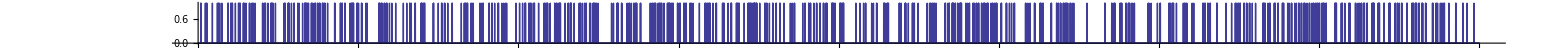

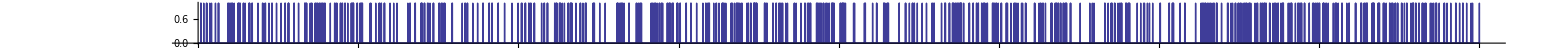

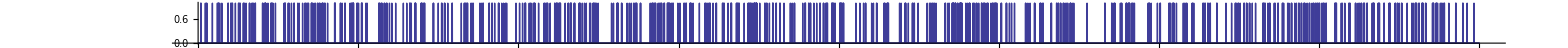

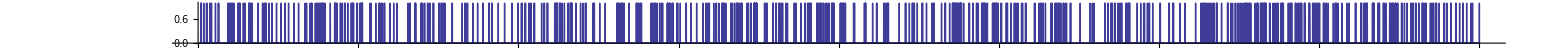

```mathematica
Display2Gate[TimeInfo[WideLF WideRB,5,0],TimeInfo[WideLF,5,1]]
Display2Gate[TimeInfo[WideLF WideRB,5,0],TimeInfo[WideRB,5,1]]
Display2Gate[TimeInfo[NarrowLF NarrowRB,5,0],TimeInfo[NarrowLF,5,1]]
Display2Gate[TimeInfo[NarrowLF NarrowRB,5,0],TimeInfo[NarrowRB,5,1]]
```

```mathematica
(* TDC *)
TDC[start_,end_,delay_,chop_]:=(countstarted=0;
count=0;
DeleteCases[Table[
Which[
And[start[[i]]≥ 1, end[[i]]==0],count=-delay;countstarted=1;-1,
And[start[[i]]≥ 1,end[[i]]≥ 1],0,
And[start[[i]]==0,end[[i]]≥ 1],If[countstarted==1,countstarted=0;If[count+1>chop,-1,count+1],-1],
And[start[[i]]==0,end[[i]]==0],count++;-1
],{i,1,Length[start]}] ,-1])
```

```mathematica
TDCLFw=TDC[TimeInfo[WideLF WideRB,5,0],TimeInfo[WideLF,5,1],5,9]
TDCRBw=TDC[TimeInfo[WideLF WideRB,5,0],TimeInfo[WideRB,5,1],5,9]
TDCLFn=TDC[TimeInfo[NarrowLF NarrowRB,5,0],TimeInfo[NarrowLF,5,1],5,5];
TDCRBn=TDC[TimeInfo[NarrowLF NarrowRB,5,0],TimeInfo[NarrowRB,5,1],5,5];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-4,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,-2,0,0,0,0,0,0,-3,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,-3,0,0,0,0,-4,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-3,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,0,-3,0,0,0,0,0,0,0,0,0,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-3,0,0,0,0,0,0,0,0,0,0,-3,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,-4,0,-4,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,0}

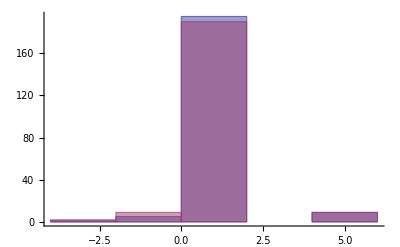

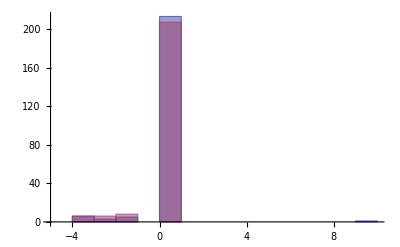

```mathematica
Histogram[{TDCLFn,TDCRBn},20,PlotRange->{{-10,10},{0,All}}]
Histogram[{TDCLFw,TDCRBw},100(*,PlotRange->{{-10,10},{0,All}}*)]
```